# Octahedral Group

### Author

Eric W. Weisstein
January 15, 2019

This notebook downloaded from http://mathworld.wolfram.com/notebooks/GroupTheory/OctahedralGroup.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/OctahedralGroup.html.

©2019 Wolfram Research, Inc. except for portions noted otherwise

## O

```mathematica
FiniteGroupData["O"]
```

{CrystallographicPointGroup,30}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup","O"}]
```

{CrystallographicPointGroup,30}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",30},"IsomorphicGroups"]
```

{Tetrahedral,{24,4},{CrystallographicPointGroup,31},{SymmetricGroup,4}}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",30},"AlternateStandardNames"]
```

{S4,Sym(4)}

bug(365915)

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",30},"Order"]
```

24

```mathematica
FiniteGroupData["O","AlternateStandardNames"]
```

{S4,Sym(4)}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",30},"Notation"]
```

O

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",30},"Classes"]
```

{Nonabelian,Nonalternating,Noncyclic,Nonperfect,Nonsimple,Nonsporadic,Solvable,Symmetric,Transitive}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",30},"ConjugacyClasses"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",30},"ConjugacyClassSizes"]
```

{1,8,3,6,6}

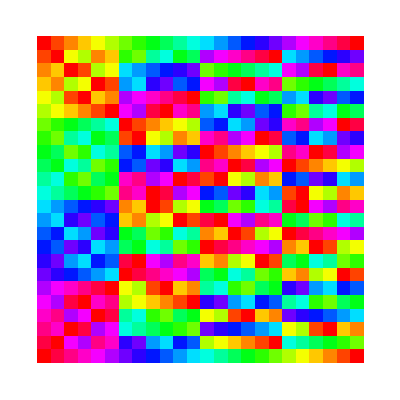
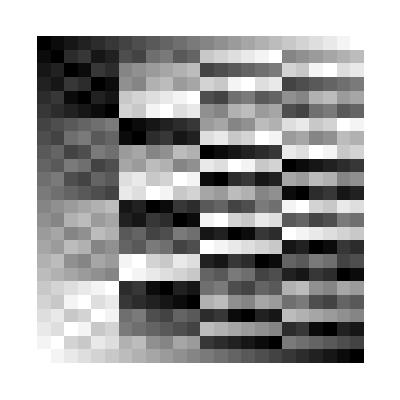

```mathematica
ArrayPlot[FiniteGroupData[{"CrystallographicPointGroup",30},"MultiplicationTable"],ColorFunction->#]&/@{Hue,GrayLevel}
```

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",30},"CayleyGraph"]
```

-Graphics-

```mathematica
UndirectedGraph[%]//ToEntity
```

truncated octahedral graph

```mathematica
spacerep=FiniteGroupData[{"CrystallographicPointGroup",30},"SpaceRepresentation"]
```

{{{1,0,0},{0,1,0},{0,0,1}},{{0,0,1},{1,0,0},{0,1,0}},{{0,0,-1},{1,0,0},{0,-1,0}},{{0,0,1},{-1,0,0},{0,-1,0}},{{0,0,-1},{-1,0,0},{0,1,0}},{{0,1,0},{0,0,1},{1,0,0}},{{0,1,0},{0,0,-1},{-1,0,0}},{{0,-1,0},{0,0,-1},{1,0,0}},{{0,-1,0},{0,0,1},{-1,0,0}},{{1,0,0},{0,-1,0},{0,0,-1}},{{-1,0,0},{0,1,0},{0,0,-1}},{{-1,0,0},{0,-1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,-1}},{{0,-1,0},{-1,0,0},{0,0,-1}},{{0,0,1},{0,-1,0},{1,0,0}},{{0,0,-1},{0,-1,0},{-1,0,0}},{{-1,0,0},{0,0,1},{0,1,0}},{{-1,0,0},{0,0,-1},{0,-1,0}},{{1,0,0},{0,0,-1},{0,1,0}},{{0,0,1},{0,1,0},{-1,0,0}},{{0,-1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,-1,0}},{{0,0,-1},{0,1,0},{1,0,0}},{{0,1,0},{-1,0,0},{0,0,1}}}

```mathematica
matrixrep=FiniteGroupData[{"CrystallographicPointGroup",30},"MatrixRepresentation"]
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}},{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},{{1,0,0,0},{0,0,1,0},{0,0,0,1},{0,1,0,0}},{{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}},{{0,1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}},{{0,1,0,0},{0,0,1,0},{1,0,0,0},{0,0,0,1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}},{{0,1,0,0},{0,0,0,1},{1,0,0,0},{0,0,1,0}},{{0,1,0,0},{0,0,0,1},{0,0,1,0},{1,0,0,0}},{{0,0,1,0},{1,0,0,0},{0,1,0,0},{0,0,0,1}},{{0,0,1,0},{1,0,0,0},{0,0,0,1},{0,1,0,0}},{{0,0,1,0},{0,1,0,0},{1,0,0,0},{0,0,0,1}},{{0,0,1,0},{0,1,0,0},{0,0,0,1},{1,0,0,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},{{0,0,1,0},{0,0,0,1},{0,1,0,0},{1,0,0,0}},{{0,0,0,1},{1,0,0,0},{0,1,0,0},{0,0,1,0}},{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}},{{0,0,0,1},{0,1,0,0},{1,0,0,0},{0,0,1,0}},{{0,0,0,1},{0,1,0,0},{0,0,1,0},{1,0,0,0}},{{0,0,0,1},{0,0,1,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}}

```mathematica
permutationrep=FiniteGroupData[{"CrystallographicPointGroup",30},"PermutationRepresentation"]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",30},"ElementNames"]
```

{E,C_(3a),C_(3b),C_(3c),C_(3d),C_(3a)^2,C_(3b)^2,C_(3c)^2,C_(3d)^2,C_2^x,C_2^y,C_2^z,C_2^(x+y),C_2^(x-y),C_2^(x+z),C_2^(x-z),C_2^(y+z),C_2^(y-z),C_4^x,C_4^y,C_4^z,C_4^x3,C_4^y3,C_4^z3}

```mathematica
Dimensions[mt=FiniteGroupData[{"CrystallographicPointGroup",30},"MultiplicationTable"]]
```

{24,24}

```mathematica
mt==With[{m=spacerep},Outer[Dot,m,m,1]/.Thread[m->Range[Length[m]]]]
```

False

```mathematica
mt==With[{m=matrixrep},Outer[Dot,m,m,1]/.Thread[m->Range[Length[m]]]]
```

False

```mathematica
Transpose[mt]==With[{m=permutationrep},Outer[PermutationReplace,m,m,1]/.Thread[m->Range[Length[m]]]]
```

True

```mathematica
mt==With[{m=permutationrep},Outer[Part,m,m,1]/.Thread[m->Range[Length[m]]]]
```

True

## O_h

```mathematica
FiniteGroupData["Oh"]
```

Octahedral

```mathematica
FiniteGroupData["Octahedral","IsomorphicGroups"]
```

{{48,8},{CrystallographicPointGroup,32},{DirectProduct,{{SymmetricGroup,4},{CyclicGroup,2}}}}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup","Oh"}]
```

{CrystallographicPointGroup,32}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",32}]
```

{CrystallographicPointGroup,32}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",32},"IsomorphicGroups"]
```

{Octahedral,{48,8},{DirectProduct,{{SymmetricGroup,4},{CyclicGroup,2}}}}

```mathematica
FiniteGroupData[{"CrystallographicPointGroup",32},"AlternateStandardNames"]
```

{Oh}

```mathematica
FiniteGroupData["Octahedral","AlternateStandardNames"]
```

{Oh}

bug(365923)

```mathematica
FiniteGroupData["Octahedral","Notation"]
```

O_h

```mathematica
FiniteGroupData["Octahedral","ElementNames"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Octahedral","Classes"]
```

{Nonabelian,Nonalternating,Noncyclic,Nonperfect,Nonsimple,Nonsporadic,Nonsymmetric,Solvable,Transitive}

```mathematica
FiniteGroupData["Octahedral","ConjugacyClasses"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Octahedral","ConjugacyClassSizes"]
```

Missing[NotAvailable]

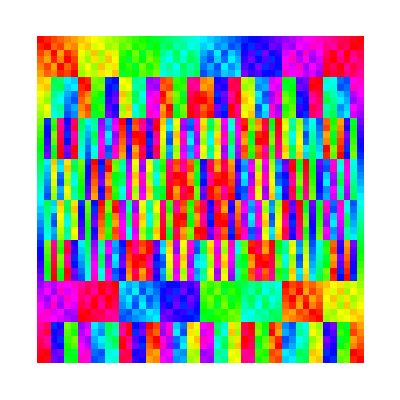
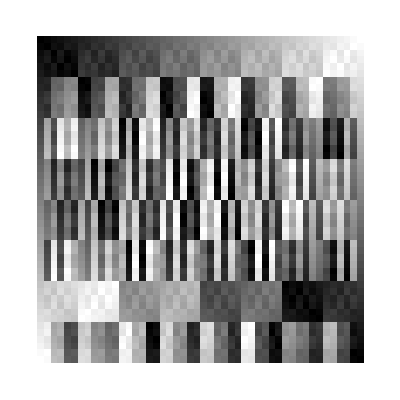

```mathematica
ArrayPlot[FiniteGroupData["Octahedral","MultiplicationTable"],ColorFunction->#]&/@{Hue,GrayLevel}
```

```mathematica
FiniteGroupData["Octahedral","CayleyGraph"]
```

-Graphics-

```mathematica
UndirectedGraph[%]//ToEntity//Head
```

ToEntity

```mathematica
spacerep=FiniteGroupData["Octahedral","SpaceRepresentation"]
```

{{{1,0,0},{0,1,0},{0,0,1}},{{0,0,1},{1,0,0},{0,1,0}},{{0,0,-1},{1,0,0},{0,-1,0}},{{0,0,1},{-1,0,0},{0,-1,0}},{{0,0,-1},{-1,0,0},{0,1,0}},{{0,1,0},{0,0,1},{1,0,0}},{{0,1,0},{0,0,-1},{-1,0,0}},{{0,-1,0},{0,0,-1},{1,0,0}},{{0,-1,0},{0,0,1},{-1,0,0}},{{1,0,0},{0,-1,0},{0,0,-1}},{{-1,0,0},{0,1,0},{0,0,-1}},{{-1,0,0},{0,-1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,-1}},{{0,-1,0},{-1,0,0},{0,0,-1}},{{0,0,1},{0,-1,0},{1,0,0}},{{0,0,-1},{0,-1,0},{-1,0,0}},{{-1,0,0},{0,0,1},{0,1,0}},{{-1,0,0},{0,0,-1},{0,-1,0}},{{1,0,0},{0,0,-1},{0,1,0}},{{0,0,1},{0,1,0},{-1,0,0}},{{0,-1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,-1,0}},{{0,0,-1},{0,1,0},{1,0,0}},{{0,1,0},{-1,0,0},{0,0,1}},{{-1,0,0},{0,-1,0},{0,0,-1}},{{0,-1,0},{0,0,-1},{-1,0,0}},{{0,-1,0},{0,0,1},{1,0,0}},{{0,1,0},{0,0,1},{-1,0,0}},{{0,1,0},{0,0,-1},{1,0,0}},{{0,0,-1},{-1,0,0},{0,-1,0}},{{0,0,1},{-1,0,0},{0,1,0}},{{0,0,-1},{1,0,0},{0,1,0}},{{0,0,1},{1,0,0},{0,-1,0}},{{-1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,-1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,-1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,-1,0},{-1,0,0},{0,0,1}},{{1,0,0},{0,0,-1},{0,-1,0}},{{0,0,-1},{0,1,0},{-1,0,0}},{{0,0,1},{0,1,0},{1,0,0}},{{1,0,0},{0,0,1},{0,1,0}},{{-1,0,0},{0,0,-1},{0,1,0}},{{0,0,1},{0,-1,0},{-1,0,0}},{{0,-1,0},{1,0,0},{0,0,-1}},{{-1,0,0},{0,0,1},{0,-1,0}},{{0,0,-1},{0,-1,0},{1,0,0}},{{0,1,0},{-1,0,0},{0,0,-1}}}

```mathematica
matrixrep=FiniteGroupData["Octahedral","MatrixRepresentation"]
```

{{{1,0,0},{0,1,0},{0,0,1}},{{0,0,1},{1,0,0},{0,1,0}},{{0,0,-1},{1,0,0},{0,-1,0}},{{0,0,1},{-1,0,0},{0,-1,0}},{{0,0,-1},{-1,0,0},{0,1,0}},{{0,1,0},{0,0,1},{1,0,0}},{{0,1,0},{0,0,-1},{-1,0,0}},{{0,-1,0},{0,0,-1},{1,0,0}},{{0,-1,0},{0,0,1},{-1,0,0}},{{1,0,0},{0,-1,0},{0,0,-1}},{{-1,0,0},{0,1,0},{0,0,-1}},{{-1,0,0},{0,-1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,-1}},{{0,-1,0},{-1,0,0},{0,0,-1}},{{0,0,1},{0,-1,0},{1,0,0}},{{0,0,-1},{0,-1,0},{-1,0,0}},{{-1,0,0},{0,0,1},{0,1,0}},{{-1,0,0},{0,0,-1},{0,-1,0}},{{1,0,0},{0,0,-1},{0,1,0}},{{0,0,1},{0,1,0},{-1,0,0}},{{0,-1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,-1,0}},{{0,0,-1},{0,1,0},{1,0,0}},{{0,1,0},{-1,0,0},{0,0,1}},{{-1,0,0},{0,-1,0},{0,0,-1}},{{0,-1,0},{0,0,-1},{-1,0,0}},{{0,-1,0},{0,0,1},{1,0,0}},{{0,1,0},{0,0,1},{-1,0,0}},{{0,1,0},{0,0,-1},{1,0,0}},{{0,0,-1},{-1,0,0},{0,-1,0}},{{0,0,1},{-1,0,0},{0,1,0}},{{0,0,-1},{1,0,0},{0,1,0}},{{0,0,1},{1,0,0},{0,-1,0}},{{-1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,-1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,-1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,-1,0},{-1,0,0},{0,0,1}},{{1,0,0},{0,0,-1},{0,-1,0}},{{0,0,-1},{0,1,0},{-1,0,0}},{{0,0,1},{0,1,0},{1,0,0}},{{1,0,0},{0,0,1},{0,1,0}},{{-1,0,0},{0,0,-1},{0,1,0}},{{0,0,1},{0,-1,0},{-1,0,0}},{{0,-1,0},{1,0,0},{0,0,-1}},{{-1,0,0},{0,0,1},{0,-1,0}},{{0,0,-1},{0,-1,0},{1,0,0}},{{0,1,0},{-1,0,0},{0,0,-1}}}

```mathematica
matrixrep==spacerep
```

True

```mathematica
permutationrep=FiniteGroupData["Octahedral","PermutationRepresentation"]
```

{{1,2,3,4,5,6,7,8},{1,2,6,5,4,3,7,8},{1,4,3,2,5,8,7,6},{1,4,8,5,2,3,7,6},{1,5,6,2,4,8,7,3},{1,5,8,4,2,6,7,3},{2,1,4,3,6,5,8,7},{2,1,5,6,3,4,8,7},{2,3,4,1,6,7,8,5},{2,3,7,6,1,4,8,5},{2,6,5,1,3,7,8,4},{2,6,7,3,1,5,8,4},{3,2,1,4,7,6,5,8},{3,2,6,7,4,1,5,8},{3,4,1,2,7,8,5,6},{3,4,8,7,2,1,5,6},{3,7,6,2,4,8,5,1},{3,7,8,4,2,6,5,1},{4,1,2,3,8,5,6,7},{4,1,5,8,3,2,6,7},{4,3,2,1,8,7,6,5},{4,3,7,8,1,2,6,5},{4,8,5,1,3,7,6,2},{4,8,7,3,1,5,6,2},{5,1,2,6,8,4,3,7},{5,1,4,8,6,2,3,7},{5,6,2,1,8,7,3,4},{5,6,7,8,1,2,3,4},{5,8,4,1,6,7,3,2},{5,8,7,6,1,4,3,2},{6,2,1,5,7,3,4,8},{6,2,3,7,5,1,4,8},{6,5,1,2,7,8,4,3},{6,5,8,7,2,1,4,3},{6,7,3,2,5,8,4,1},{6,7,8,5,2,3,4,1},{7,3,2,6,8,4,1,5},{7,3,4,8,6,2,1,5},{7,6,2,3,8,5,1,4},{7,6,5,8,3,2,1,4},{7,8,4,3,6,5,1,2},{7,8,5,6,3,4,1,2},{8,4,1,5,7,3,2,6},{8,4,3,7,5,1,2,6},{8,5,1,4,7,6,2,3},{8,5,6,7,4,1,2,3},{8,7,3,4,5,6,2,1},{8,7,6,5,4,3,2,1}}

```mathematica
Dimensions[mt=FiniteGroupData["Octahedral","MultiplicationTable"]]
```

{48,48}

```mathematica
mt==With[{m=spacerep},Outer[Dot,m,m,1]/.Thread[m->Range[Length[m]]]]
```

False

```mathematica
mt==With[{m=permutationrep},Outer[PermutationReplace,m,m,1]/.Thread[m->Range[Length[m]]]]
```

True

```mathematica
Transpose[mt]==With[{m=permutationrep},Outer[PermutationReplace,m,m,1]/.Thread[m->Range[Length[m]]]]
```

False

```mathematica
mt==With[{m=permutationrep},Outer[Part,m,m,1]/.Thread[m->Range[Length[m]]]]
```

False

jose 2018-01-15: The multiplication table we currently give is based on the order given by a permutation representation of the group, while the list of matrices has been given is some other order. I need to find the reordering that moves one to the other, but this is not simple, so I'd prefer not to do it right now.

## O (pre-FiniteGroupData)

```mathematica
orules=Thread[PointGroup["O"]->Range[24]];
```

General::spell: Possible spelling error: new symbol name "orules" is similar to existing symbols {arules, irules, mrules, nrules, prules, rules}. More…

### Group

```mathematica
GroupQ[PointGroup["O"]]//Timing
```

{1.84 Second,True}

### Abelian

```mathematica
AbelianGroupQ[PointGroup["O"]]
```

False

### Conjugacy Classes

```mathematica
ConjugacyClasses[PointGroup["O"]]/.rules
```

{{24},{1,4,21},{2,3,5,10,14,20},{8,11,15,17,22,23},{6,7,9,12,13,16,18,19}}

```mathematica
Length/@%
```

{1,3,6,6,8}

### Subgroups

```mathematica
(sub=Subgroups[PointGroup["O"]]/.orules)//Timing
```

$Aborted

```mathematica
Length/@sub
```

### Multiplication Table

```mathematica
Show[GraphicsArray[ListDensityPlot[Reverse@GroupMultiplicationTable[PointGroup["O"],orules][[1]],ColorFunction->#,Frame->False,Mesh->True,
PlotLabel->TraditionalForm[O],
DisplayFunction->Identity]&/@{Hue,GrayLevel}]]
```

⁃GraphicsArray⁃

### Polyhedra

Vectors for the octahedral Group.

```mathematica
Vector[Cube]={1,1,1};
Vector[Octahedron]={1,0,0};
Vector[Cuboctahedron]={1,0,1};
Vector[TruncatedOctahedron]={1, 0, 2};
Vector[TruncatedCube]={1,1,Sqrt[2]-1};
Vector[SmallRhombicuboctahedron]={1,1,Sqrt[2]+1};
Vector[SnubCube]={1,Root[-1+#1+#1^2+#1^3&,1],Root[-1+3 #1+#1^2+#1^3&,1]};
```

```mathematica
polys=#[[1,1,1]]&/@DownValues[Vector]
```

{Cube,Cuboctahedron,Octahedron,SmallRhombicuboctahedron,SnubCube,TruncatedCube,TruncatedOctahedron}

```mathematica
<<ConvexHull`
```

```mathematica
Show[GraphicsArray[Partition[
Graphics3D[#,Boxed->False]&/@Function[v,ConvexHull3D[Union[Chop/@Simplify[#.v&/@PointGroup["O"]]]]]/@(N/@Vector/@polys),
4,4,{1,1},{}]
]]//Timing
```

{2.05 Second,⁃GraphicsArray⁃}

### Cycle Graph

```mathematica
m=MaximalGraphCycles[PointGroup["O"]]
```

{{24,2},{24,3},{24,5},{24,10},{24,14},{24,20},{24,6,13},{24,7,9},{24,12,18},{24,16,19},{24,8,1,17},{24,11,4,15},{24,22,21,23}}

```mathematica
Split[Sort[Flatten[Rest/@m]]]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23}}

```mathematica
ShowLabeledGraph[RadialEmbedding[CycleGraph[PointGroup["O"]]]]
```

⁃Graphics⁃

## O_h (pre-FiniteGroupData)

```mathematica
ohrules=Thread[PointGroup["Oh"]->Range[48]];
```

General::spell1: Possible spelling error: new symbol name "ohrules" is similar to existing symbol "orules". More…

### Group

```mathematica
GroupQ[PointGroup["Oh"]]//Timing
```

{14.13 Second,True}

### Abelian

```mathematica
AbelianGroupQ[PointGroup["Oh"]]
```

False

### Conjugacy Classes

```mathematica
(classes=ConjugacyClasses[PointGroup["Oh"]]/.ohrules)//Timing
```

{1.48 Second,{{24},{48},{25,28,45},{21,4,1},{26,27,29,34,38,44},{23,22,17,15,11,8},{20,14,10,5,3,2},{32,35,39,41,46,47},{19,18,16,13,12,9,7,6},{30,31,33,36,37,40,42,43}}}

```mathematica
Length/@classes
```

{1,1,3,3,6,6,6,6,8,8}

### Subgroups

```mathematica
SubgroupQ[Sequence@@PointGroup/@{"O","Oh"}]//Timing
```

{1.79 Second,True}

```mathematica
(subg=Subgroups[PointGroup["Oh"]]/.ohrules)//Timing
```

$Aborted

```mathematica
Length/@subg
```

### Multiplication Table

```mathematica
Show[GraphicsArray[ListDensityPlot[Reverse@GroupMultiplicationTable[PointGroup["Oh"],ohrules][[1]],
DisplayFunction->Identity,
PlotLabel->TraditionalForm[Subscript[O, h]],ColorFunction->#,Frame->False,Mesh->False]&/@{Hue,GrayLevel}]]
```

⁃GraphicsArray⁃

### Polyhedra

Vectors for the octahedral Group.

```mathematica
Vector48[GreatRhombicuboctahedron]={1,3-Sqrt[2],Sqrt[2]-1};
```

```mathematica
polys=#[[1,1,1]]&/@DownValues[Vector48]
```

{GreatRhombicuboctahedron}

```mathematica
<<ConvexHull`
```

```mathematica
Show[GraphicsArray[Partition[
Graphics3D[#,Boxed->False]&/@Function[v,ConvexHull3D[Union[Chop/@Simplify[#.v&/@PointGroup["Oh"]]]]]/@(N/@Vector48/@polys),
5,5,{1,1},{}]
]]//Timing
```

{1.52 Second,⁃GraphicsArray⁃}

### Cycle Graph

```mathematica
m=MaximalGraphCycles[PointGroup["Oh"]]
```

{{48,1},{48,2},{48,3},{48,4},{48,5},{48,10},{48,14},{48,20},{48,21},{48,26},{48,27},{48,29},{48,34},{48,38},{48,44},{48,8,25,17},{48,11,28,15},{48,22,45,23},{48,32,25,41},{48,35,28,39},{48,46,45,47},{48,6,37,24,30,13},{48,7,33,24,31,9},{48,12,42,24,36,18},{48,16,43,24,40,19}}

```mathematica
Split[Sort[Flatten[Rest/@m]]]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24,24,24,24},{25,25},{26},{27},{28,28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45,45},{46},{47}}

```mathematica
ShowLabeledGraph[RadialEmbedding[CycleGraph[PointGroup["Oh"]]]]
```

⁃Graphics⁃